```mathematica
SetDirectory["D:\\newLight3\\organisms"]
```

D:\newLight3\organisms

```mathematica
SetDirectory["D:\\grafiliv - stayin alive\\organisms"]
```

D:\grafiliv - stayin alive\organisms

```mathematica
GetOrganism[orgNo_]:=With[{path=StringForm["org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
GenomeSize[orgNo_]:=With[{
g ="genome"/.GetOrganism[orgNo],
n="nervesystem"/.GetOrganism[orgNo]
},
{Length["vertices"/.n]+Length["links"/.n],Length["vertices"/.g]+Length["links"/.g]}
]
```

```mathematica
GetParent[orgNo_]:=Module[{path,g,n,s,i},
Quiet[
path = StringForm["org``.json",orgNo];
{g,n,s,i}=Import[path//ToString];
"parent"/.i
]
]
```

```mathematica
oMax=Length[FileNames[]]-1;
δo=Ceiling[oMax/1000];
orgs=Table[frame,{frame,0,oMax,δo}];
data=ParallelMap[GenomeSize,orgs];
```

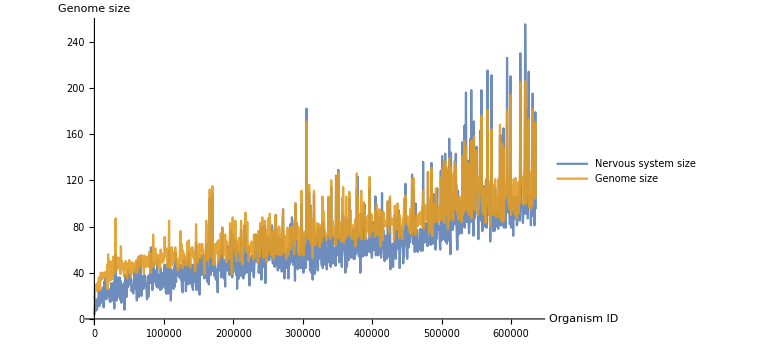

```mathematica
ListLinePlot[data//Transpose,DataRange->{0,oMax},AxesLabel->{"Organism ID","Genome size"}, PlotLegends->Placed[{"Nervous system size","Genome size"},Below], PlotRange->Full,PlotStyle->Opacity[0.9],ImageSize->Large]
```

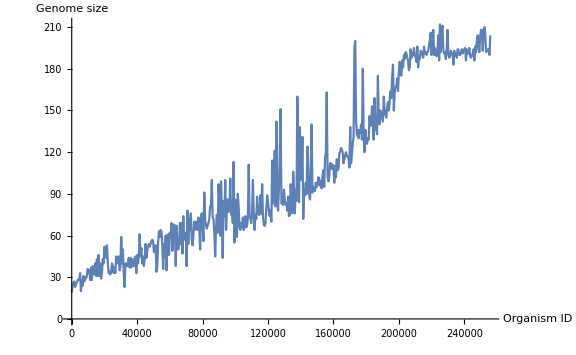

```mathematica
ancestors=NestWhileList[GetParent,oMax,#>0&];
data2=ParallelMap[GenomeSize,ancestors]//Reverse;
```

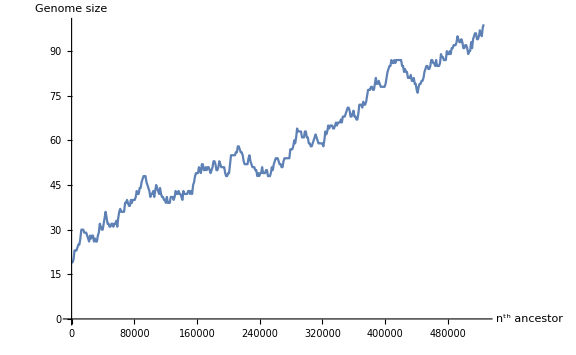

```mathematica
ListLinePlot[data2,DataRange->{0,oMax},AxesLabel->{"n^th ancestor","Genome size"}, ImageSize->Large]
```